# Hydrodynamik

Simon : Stoppuhr + Hahn

Mirco : Messzylinder

```mathematica
ClearAll["Global`*"];
```

```mathematica
λ = 1/60/1000/1000;
```

```mathematica
l = 0.2;
```

```mathematica
g = 9.81;
```

```mathematica
ρ = 998;
```

```mathematica
QH[r_, h_, ϵ_] = ρ*g*h/(8*ϵ*l/(π*r^4));
```

```mathematica
QE[r_, h_, ϵ_] = (Sqrt[16*π^2*ϵ^2*l^2+1.14*ρ*π^2*ρ*g*h*r^4]-4*π*ϵ*l)/(1.14*ρ);
```

```mathematica
r =(r /.Solve[q==QE[r,h,ϵ], r])
```

{-(1. (0.0117743 q^2+0.00005202 q ϵ-1.61583×10^-23 ϵ^2)^(1/4))/h^(1/4),-((0.+1. ⅈ) (0.0117743 q^2+0.00005202 q ϵ-1.61583×10^-23 ϵ^2)^(1/4))/h^(1/4),((0.+1. ⅈ) (0.0117743 q^2+0.00005202 q ϵ-1.61583×10^-23 ϵ^2)^(1/4))/h^(1/4),((0.0117743 q^2+0.00005202 q ϵ-1.61583×10^-23 ϵ^2)^(1/4))/h^(1/4)}

```mathematica
rrr=r[[1]]^(4)
```

(1. (0.0117743 q^2+0.00005202 q ϵ-1.61583×10^-23 ϵ^2))/h

## Temperatur

```mathematica
T = {{15.00, 18.6}, {15.15, 19.00}, {15.30, 19.3}, {15.45, 19.7}, {16.00, 20.2}, {16.15, 20.7}};
```

## Aufgabe 2

```mathematica
h = #/100&/@{50,59.7,55,46.4,38.7,31.6,20.6};
```

```mathematica
f = #*λ&/@{33,38.5,36,31,26,21,14};
```

```mathematica
a = ListPlot[Table[{h[[i]], f[[i]]}, {i, 1, Length[h]}]];
```

```mathematica
ρ = 998;
```

```mathematica
g = 9.81;
```

```mathematica
r = 0.505/1000;
```

```mathematica
l = 0.2;
```

```mathematica
ϵ = 0.0010266;
```

```mathematica
b = Plot[QH[r, h, ϵ], {h, 0, 0.7}];
```

```mathematica
c = Plot[QE[r,h,ϵ], {h, 0, 0.7}];
```

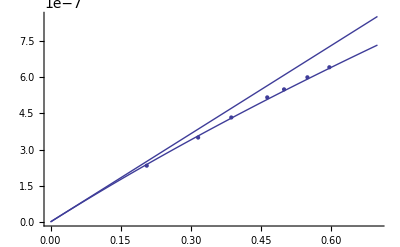

```mathematica
Show[{a,b,c}]
```

## Aufgabe 3

```mathematica
ϵ = 0.0010140;
```

```mathematica
h = 50/100;
```

```mathematica
d = #/1000&/@{1.01,0.61,0.84,1.23};
```

```mathematica
Q = #*λ&/@{33,5,17.25,65}//N
```

{5.5×10^-7,8.33333×10^-8,2.875×10^-7,1.08333×10^-6}

```mathematica
Table[QH[d[[i]]/2,h,0.001037], {i, 1, Length[d]}]
```

{6.02818×10^-7,8.02084×10^-8,2.88415×10^-7,1.32593×10^-6}

```mathematica
Table[QE[d[[i]]/2,h,0.001037], {i, 1, Length[d]}]
```

{5.39329×10^-7,7.88514×10^-8,2.72238×10^-7,1.07411×10^-6}

```mathematica
rr[qqq_] = 8*ϵ*l*qqq/π/(ρ*g*h)
```

1.05497×10^-7 qqq

```mathematica
d
```

{0.00101,0.00061,0.00084,0.00123}

```mathematica
Solve[QE, r]
```

Solve::ivar: 0.000505 is not a valid variable.

Solve[QE,0.000505]

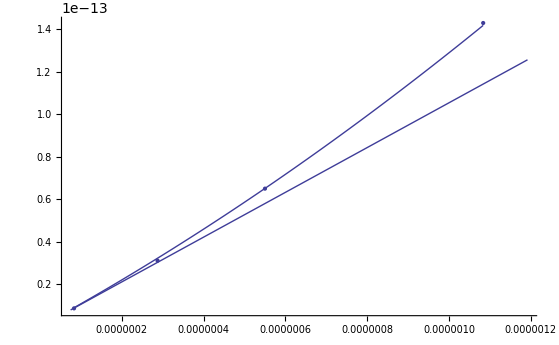

```mathematica
Show[ListPlot[Table[{Q[[i]],(d[[i]]/2)^4}, {i,1,Length[d]}]], Plot[rr[qqq], {qqq, Min[Q]*0.9, Max[Q]*1.1}], Plot[rrr, {q, Min[Q], Max[Q]}]]
```

## Aufgabe 4

```mathematica
ϵ = 0.0010041;
```

```mathematica
d1 = 1.01/1000;
```

```mathematica
d2 = 1.00/1000;
```

```mathematica
h = 0.5;
```

```mathematica
R[qq_] = ρ*g*h/qq
```

4895.19/qq

### Parallel (±2.5 ml/min)

```mathematica
Qp = 68*λ;
```

```mathematica
R[Qp]
```

4.31929×10^9

### Einzeln (±0.5 ml/min)

```mathematica
Q1 = 33*λ;
```

```mathematica
Q2 = 33*λ;
```

```mathematica
R[Q1]
```

8.90035×10^9

### Seriell(±0.25 ml/min)

```mathematica
Qs = 17.25*λ;
```

```mathematica
R[Qs]
```

1.70267×10^10

```mathematica
sh = 0.1;
```

```mathematica
sQ = 0.5;
```

```mathematica
s = Sqrt[(ρ*g/Qs)^2*sh^2 + (ρ*g*h/Qs^2)^2*sQ^2]
```

2.96117×10^16

## Aufgabe 5

```mathematica
ϵ=0.00098946;
```

```mathematica
r = 1.99/2/1000;
```

```mathematica
h = #/100&/@{59.7,42.8,28,11.8,35.2,50.5,20.4,15.4,25.5,30.8};
```

```mathematica
Q = #*λ&/@{274,242.5,190,97.5,220,256,150,120,178,202.5};
```

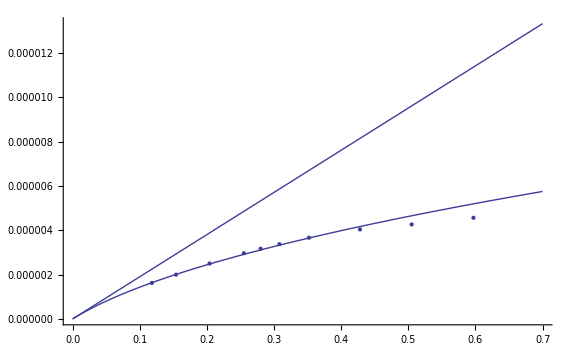

```mathematica
Show[ListPlot[Table[{h[[i]], Q[[i]]}, {i,1,Length[h]}]], Plot[QH[r,h,ϵ],{h,0,0.7}],Plot[QE[r,h,ϵ],{h,0,0.7}]]
```

```mathematica
q = QH[r,0.5,ϵ]
```

9.52124×10^-6

```mathematica
k = q*2*ρ/ϵ/π/r
```

6144.45